R1 = R1

T1 = T1

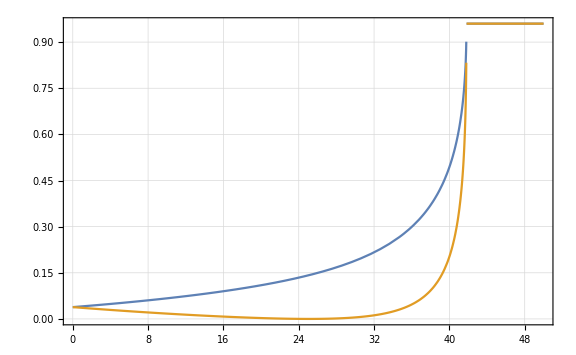

angle = 40, rs = 0.493762, rp = 0.202454

```mathematica
ClearAll["Global`*"];

(* Vacuum *)
n0=1;

(* Glass *)
n1=1.5;

n2=1;

(* First boundary *)
r1=(n0-n1)^2/(n0+n1)^2;
t1=4*n0*n1/(n0+n1)^2;

Print["R1 = ", R1];
Print["T1 = ", T1];

(* =================== *)

rs[a_]:=t1*Abs[(n1*Cos[a]-n2*Sqrt[1-((n1/n2)*Sin[a])])/(n1*Cos[a]+n2*Sqrt[1-((n1/n2)*Sin[a])])]^2;
rp[a_]:=t1*Abs[(n1*Sqrt[1-((n1/n2)*Sin[a])]-n2*Cos[a])/(n1*Sqrt[1-((n1/n2)*Sin[a])]+n2*Cos[a])]^2;

Print[Plot[{rs[x Degree],rp[x Degree]},{x,0,50}, PlotRange->All, Frame -> True, GridLines -> Automatic, ImageSize->Large]];

angle =40;
Print["angle = ", angle, ", rs = ", rs[angle Degree], ", rp = ", rp[angle Degree]];
```